# One Dimensional FEM computation

## Finite element data

```mathematica
Nodes={
{0.,0},
{4,0},
{2*4,0},
{3*4,0},
{4*4,0}
};
ElemNodes={
{1,2},
{2,3},
{3,4},
{4,5}
};
ElemOrders={
1,2,3,5};
ElemEquations=ElemNodes;
NEquations=Length[Nodes]+1;
For[el=1,el<=Length[ElemNodes],el++,
For[order=2,order<=ElemOrders[[el]],order++,AppendTo[ElemEquations[[el]],NEquations++]]
]
ElemEquations
NEquations--;
NEquations
```

{{1,2},{2,3,6},{3,4,7,8},{4,5,9,10,11,12}}

12

## Geometry

```mathematica
XShape={(1-ksi)/2,(1+ksi)/2}
X[el_]:=Block[{x1,x2,val},
x1=Nodes[[ElemNodes[[el,1]]]];
x2=Nodes[[ElemNodes[[el,2]]]];
val=XShape[[1]]x1+XShape[[2]]x2;
val
]
GradX[el_]:=Block[{},
Grad[X[el],{ksi}]
]
Jac[el_]:=Norm[GradX[el]]
X[4]
GradX[1]
Jac[1]
```

{(1-ksi)/2,(1+ksi)/2}

{6 (1-ksi)+8 (1+ksi),0}

{{2},{0}}

2

## Numerical Integration

## Points and weights https://en.wikipedia.org/wiki/Gaussian_quadrature

```mathematica
<<NumericalDifferentialEquationAnalysis`;
```

```mathematica
GaussianQuadratureWeights[3,-1,1]//Transpose
```

{{-0.774597,0.,0.774597},{0.555556,0.888889,0.555556}}

```mathematica
Rules={
{{0},{2}},
{{-1/Sqrt[3],1/Sqrt[3]},{1,1}},
{{-Sqrt[3/5],0,Sqrt[3/5]},{5/9,8/9,5/9}},
{{-Sqrt[3/7-2/7Sqrt[6/5]],-Sqrt[3/7+2/7Sqrt[6/5]],Sqrt[3/7-2/7Sqrt[6/5]],Sqrt[3/7+2/7Sqrt[6/5]]},{(18+Sqrt[30])/36,(18-Sqrt[30])/36,(18+Sqrt[30])/36,(18-Sqrt[30])/36}}
};
Rules//MatrixForm
GetRule[n_] := GaussianQuadratureWeights[n,-1,1]//Transpose
```

({0} | {2}
{-1/(√3),1/(√3)} | {1,1}
{-√(3/5),0,√(3/5)} | {5/9,8/9,5/9}
{-√(3/7-(2 √(6/5))/7),-√(3/7+(2 √(6/5))/7),√(3/7-(2 √(6/5))/7),√(3/7+(2 √(6/5))/7)} | {1/36 (18+√30),1/36 (18-√30),1/36 (18+√30),1/36 (18-√30)})

```mathematica
NIntegrate`GaussKronrodRuleData[2,MachinePrecision][[1;;2]]
```

{{0.03709,0.211325,0.5,0.788675,0.96291},{0.0989899,0.245455,0.311111,0.245455,0.0989899}}

## Master element shape functions

{(1-ksi)/2,(1+ksi)/2,1-ksi^2,ksi (1-ksi^2),ksi^2 (1-ksi^2),ksi^3 (1-ksi^2),ksi^4 (1-ksi^2),ksi^5 (1-ksi^2),ksi^6 (1-ksi^2),ksi^7 (1-ksi^2),ksi^8 (1-ksi^2)}

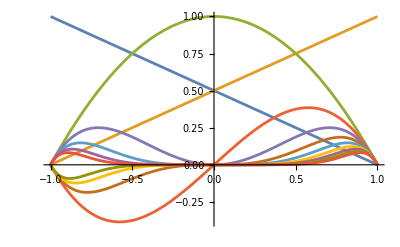

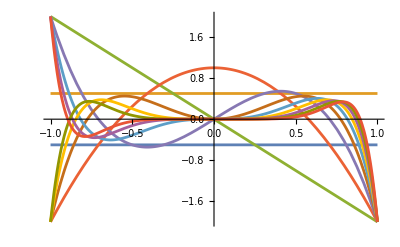

```mathematica
phimaster={(1-ksi)/2,(1+ksi)/2,1-ksi^2};
For[order=3,order<=10,order++,AppendTo[phimaster,phimaster[[-1]]ksi]]
phimaster
dphimaster=D[phimaster,ksi];
Plot[phimaster,{ksi,-1,1}]
Plot[dphimaster,{ksi,-1,1}]
```

## Element Integration

### Example integration

```mathematica
element=1;
r=GetRule[2];
np=Length[r[[1]]];
Print["npoints = ",np]
ord=ElemOrders[[element]];
Print["element order ",ord]
nfunc=ord+1;
elmat=Table[0,{nfunc},{nfunc}];
elf=Table[0,{nfunc}];
For[ip=1,ip<=np,ip++,
loc=r[[1,ip]];
w=r[[2,ip]];
phiel=phimaster[[1;;nfunc]]/.ksi->loc;
dphiel=dphimaster[[1;;nfunc]]/.ksi->loc;
Print["ksi do ponto ",loc];
Print["valor das funcoes ",phiel];
jac=Jac[element]/.ksi->loc;
dphielx=dphiel/jac;
xp=X[element]/.ksi->loc;
Print["xp = ",xp];
elmat+=Table[(dphielx[[i]]dphielx[[j]]+0*phiel[[i]]phiel[[j]])w jac,{i,nfunc},{j,nfunc}];
elf+=Table[xp[[1]] phiel[[i]]w jac,{i,nfunc}];
Print["elmat = ",elmat//Simplify//MatrixForm];
Print["fmat = ",elf//Simplify];
]
```

npoints = 2

element order 1

ksi do ponto -0.57735

valor das funcoes {0.788675,0.211325}

xp = {0.845299,0}

elmat = (0.125 | -0.125
-0.125 | 0.125)

fmat = {1.33333,0.357266}

ksi do ponto 0.57735

valor das funcoes {0.211325,0.788675}

xp = {3.1547,0}

elmat = (0.25 | -0.25
-0.25 | 0.25)

fmat = {2.66667,5.33333}

### Integration of elementstiffness

```mathematica
Stiff[el_]:=Block[{element,r,np,ord,nfunc,elmat,elf,ip,loc,w,phiel,dphiel,jac,dphielx,xp,ksi},
element=el;
ord=ElemOrders[[element]];
np=ord+1;
r=GetRule[np];
nfunc=ord+1;
elmat=Table[0,{nfunc},{nfunc}];
elf=Table[0,{nfunc}];
For[ip=1,ip<=np,ip++,
loc=r[[1,ip]];
w=r[[2,ip]];
phiel=phimaster[[1;;nfunc]]/.ksi->loc;
dphiel=dphimaster[[1;;nfunc]]/.ksi->loc;
jac=Jac[element]/.ksi->loc;
dphielx=dphiel/jac;
xp=X[element]/.ksi->loc;
elmat+=Table[(dphielx[[i]]dphielx[[j]]+phiel[[i]]phiel[[j]])w jac,{i,nfunc},{j,nfunc}];
elf+=Table[xp[[1]] phiel[[i]]w jac,{i,nfunc}];
];
{elmat//Simplify,elf//Simplify}
]
Stiff[1][[1]]//MatrixForm
Stiff[1][[2]]//MatrixForm
Stiff[2][[2]]//MatrixForm
Stiff[3][[2]]//MatrixForm
Stiff[4][[2]]//MatrixForm
```

(1.58333 | 0.416667
0.416667 | 1.58333)

(2.66667
5.33333)

(10.6667
13.3333
16.)

(18.6667
21.3333
26.6667
1.06667)

(26.6667
29.3333
37.3333
1.06667
7.46667
0.457143)

## Assembly

```mathematica
GlobMat=Table[0,{NEquations},{NEquations}];
GlobF=Table[0,{NEquations}];
element=2
eleq=ElemEquations[[element]]
neq=Length[eleq]
{elmat,elf}=Stiff[element];
For[i=1,i<=neq,i++,
gi=eleq[[i]];
GlobF[[gi]]+=elf[[i]];
For[j=1,j<=neq,j++,
gj=eleq[[j]];
GlobMat[[gi,gj]]+=elmat[[i,j]]
]
]
GlobMat//MatrixForm
GlobF//MatrixForm
```

2

{2,3,6}

3

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.58333 | 0.416667 | 0 | 0 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.416667 | 1.58333 | 0 | 0 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.33333 | 1.33333 | 0 | 0 | 3.46667 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0
10.6667
13.3333
0
0
16.
0
0
0
0
0
0)

## AssemblyFunction

```mathematica
Assemble[glob_,el_]:=Block[{elst,GlobMat,GlobF,eleq,neq,elmat,elf,i,gi,gj,j},
elst=Stiff[el];
eleq=ElemEquations[[el]];
neq=Length[eleq];
{elmat,elf}=Stiff[el];
{GlobMat,GlobF}=glob;
For[i=1,i<=neq,i++,
gi=eleq[[i]];
GlobF[[gi]]+=elf[[i]];
For[j=1,j<=neq,j++,
gj=eleq[[j]];
GlobMat[[gi,gj]]+=elmat[[i,j]]
]
];
{GlobMat,GlobF}
]
```

## Computing the global matrices

```mathematica
GlobMat=Table[0,{NEquations},{NEquations}];
GlobF=Table[0,{NEquations}];

For[el=1,el<=Length[ElemEquations],el++,
{GlobMat,GlobF}=Assemble[{GlobMat,GlobF},el]
]
GlobMat//MatrixForm
GlobF//MatrixForm
Sol=LinearSolve[GlobMat,GlobF]
```

(1.58333 | 0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.416667 | 3.16667 | 0.416667 | 0 | 0 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.416667 | 3.16667 | 0.416667 | 0 | 1.33333 | 1.33333 | -0.266667 | 0 | 0 | 0 | 0
0 | 0 | 0.416667 | 3.16667 | 0.416667 | 0 | 1.33333 | 0.266667 | 1.33333 | -0.266667 | 0.266667 | -0.114286
0 | 0 | 0 | 0.416667 | 1.58333 | 0 | 0 | 0 | 1.33333 | 0.266667 | 0.266667 | 0.114286
0 | 1.33333 | 1.33333 | 0 | 0 | 3.46667 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.33333 | 1.33333 | 0 | 0 | 3.46667 | 5.55112×10^-17 | 0 | 0 | 0 | 0
0 | 0 | -0.266667 | 0.266667 | 0 | 0 | 5.55112×10^-17 | 1.10476 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.33333 | 1.33333 | 0 | 0 | 0 | 3.46667 | -5.55112×10^-17 | 0.571429 | 0.
0 | 0 | 0 | -0.266667 | 0.266667 | 0 | 0 | 0 | -5.55112×10^-17 | 1.10476 | -2.77556×10^-17 | 0.444444
0 | 0 | 0 | 0.266667 | 0.266667 | 0 | 0 | 0 | 0.571429 | -2.77556×10^-17 | 0.520635 | 0.
0 | 0 | 0 | -0.114286 | 0.114286 | 0 | 0 | 0 | 0. | 0.444444 | 0. | 0.33824)

(2.66667
16.
32.
48.
29.3333
16.
26.6667
1.06667
37.3333
1.06667
7.46667
0.457143)

{0.658849,3.89637,7.99492,11.9817,15.,0.0418097,0.00900513,0.00319967,0.373208,0.219598,0.111962,0.0431353}

## Applying boundary condition

```mathematica
GlobMat[[1,;;]]=0;
GlobMat[[;;,1]]=0;
GlobMat[[1,1]]=1;
GlobF[[1]]=0;
nel=Length[ElemEquations];
GlobMat[[nel+1,;;]]=0;
GlobMat[[;;,nel+1]]=0;
GlobMat[[nel+1,nel+1]]=1;
GlobF[[nel+1]]=0;
GlobMat//MatrixForm
GlobF//MatrixForm
Sol=LinearSolve[GlobMat,GlobF]
Sol//N
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.16667 | 0.416667 | 0 | 0 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.416667 | 3.16667 | 0.416667 | 0 | 1.33333 | 1.33333 | -0.266667 | 0 | 0 | 0 | 0
0 | 0 | 0.416667 | 3.16667 | 0 | 0 | 1.33333 | 0.266667 | 1.33333 | -0.266667 | 0.266667 | -0.114286
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.33333 | 1.33333 | 0 | 0 | 3.46667 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.33333 | 1.33333 | 0 | 0 | 3.46667 | 5.55112×10^-17 | 0 | 0 | 0 | 0
0 | 0 | -0.266667 | 0.266667 | 0 | 0 | 5.55112×10^-17 | 1.10476 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.33333 | 0 | 0 | 0 | 0 | 3.46667 | -5.55112×10^-17 | 0.571429 | 0.
0 | 0 | 0 | -0.266667 | 0 | 0 | 0 | 0 | -5.55112×10^-17 | 1.10476 | -2.77556×10^-17 | 0.444444
0 | 0 | 0 | 0.266667 | 0 | 0 | 0 | 0 | 0.571429 | -2.77556×10^-17 | 0.520635 | 0.
0 | 0 | 0 | -0.114286 | 0 | 0 | 0 | 0 | 0. | 0.444444 | 0. | 0.33824)

(0
16.
32.
48.
0
16.
26.6667
1.06667
37.3333
1.06667
7.46667
0.457143)

{0.,3.99984,7.99552,11.7079,0.,0.00178515,0.114084,0.0694353,5.97094,3.51388,1.79128,0.690226}

{0.,3.99984,7.99552,11.7079,0.,0.00178515,0.114084,0.0694353,5.97094,3.51388,1.79128,0.690226}

## Element Solution

1

{1,2}

2

{0.,3.99984}

0.+1.99992 (1+ksi)

{0.+2 (1+ksi),0}

{{0.,0.},{0.4,0.399984},{0.8,0.799968},{1.2,1.19995},{1.6,1.59994},{2.,1.99992},{2.4,2.3999},{2.8,2.79989},{3.2,3.19987},{3.6,3.59985},{4.,3.99984}}

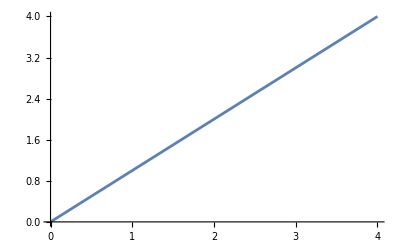

```mathematica
element=1
eleq = ElemEquations[[element]]
nfunc=ElemOrders[[element]]+1
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}]//N
elsol=Sum[phimaster[[i]]elcoef[[i]],{i,nfunc}]
elx=X[element]
elval=Table[{elx[[1]],elsol},{ksi,-1,1,1/5}]
ListPlot[elval,Joined->True]
```

## Post processing

```mathematica
ElementValues[el_,globsol_]:=Block[{element,eleq,nfunc,elcoef,elsol,elx,elval,Sol},
element=el;
Sol=globsol;
eleq = ElemEquations[[element]];
nfunc=ElemOrders[[element]]+1;
elcoef=Table[Sol[[eleq[[i]]]],{i,nfunc}];
elsol=Sum[phimaster[[i]]elcoef[[i]],{i,nfunc}];
elx=X[element];
elval=Table[{elx[[1]],elsol},{ksi,-1,1,1/5}]
]
```

```mathematica
ElementValues[1,Sol]
```

{{0.,0.},{0.4,0.399984},{0.8,0.799968},{1.2,1.19995},{1.6,1.59994},{2.,1.99992},{2.4,2.3999},{2.8,2.79989},{3.2,3.19987},{3.6,3.59985},{4.,3.99984}}

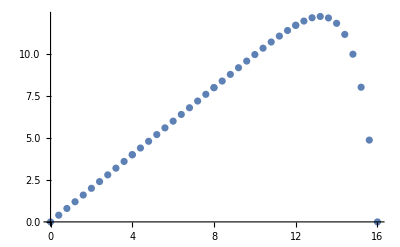

```mathematica
Allval={};
nels=Length[ElemEquations];
For[el=1,el<=nels,el++,AppendTo[Allval,ElementValues[el,Sol]]]
Allval=Flatten[Allval,1];
ListPlot[Allval,Joined->False]
```

-ⅇ^(-1/4/eps)+ⅇ^(-(-1/2+x)^2/eps)

-ⅇ^(-1/4/eps)+ⅇ^(-(-1/2+x)^2/eps)+(2 ⅇ^(-(-1/2+x)^2/eps))/eps-(4 ⅇ^(-(-1/2+x)^2/eps) (-1/2+x)^2)/eps^2

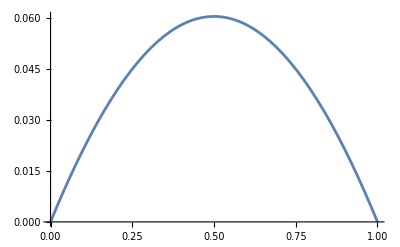

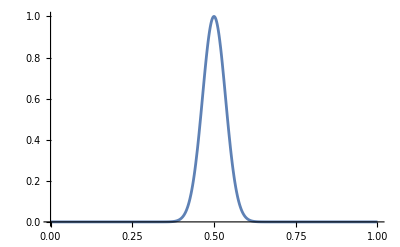

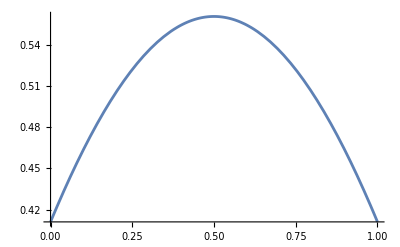

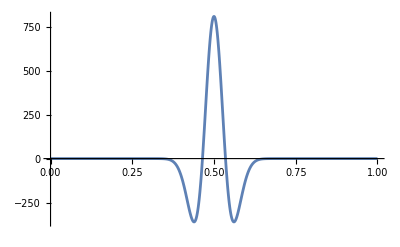

```mathematica
ClearAll[eps,x]
uex=E^(-(x-1/2)^2/eps)-E^(-(1/2)^2/eps)
f=-D[uex,x,x]+uex
Plot[uex/.eps->4,{x,0,1}]
Plot[uex/.eps->E^(-6),{x,0,1},PlotRange->{0,1}]
Plot[f/.eps->4,{x,0,1}]
Plot[f/.eps->E^(-6),{x,0,1},PlotRange->All]
```